### Start choosing the example:

```mathematica
t=22;
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7},Adjacency Matrix→{{0,1,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,1,1,0,0},{0,0,0,0,0,1,0},{0,0,0,0,0,1,1},{0,0,0,0,0,0,1},{0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1},{2,I2}},Exit Vertices and Terminal Costs→{{5,U1},{6,U2},{7,U3}},Switching Costs→{}|>

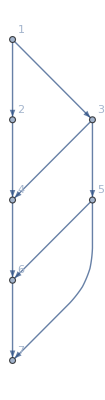

```mathematica
AdjacencyGraph[Data["Vertices List"],Data["Adjacency Matrix"],VertexLabels->"Name"]
```

### Look at the output bellow before trying to rerun!

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2,I2->2, U1-> 1,U2->1,U3->1}];//Timing//AbsoluteTiming
```

DataToEquations: Triangle inequalities for switching costs: {}
DataToEquations: Reduced: True

DataToEquations: The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 230.192 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{230.508,{244.506,Null}}

<|j1478→0,j1479→2,j1480→2,j1481→0,j1482→2,j1483→2,j1484→0,j1485→0,j1486→2,j1487→0,j1488→2,j1489→0,j1490→2,j1491→2,j1492→0,j1493→0,j1494→0,j1495→0,j1496→0,j1497→0,j1498→0,j1499→0,j1500→0,j1501→0,j1502→0,j1503→0,j1504→0,j1505→0,jt1506→0,jt1507→0,jt1508→0,jt1509→0,jt1510→0,jt1511→2,jt1512→0,jt1513→0,jt1514→0,jt1515→0,jt1516→0,jt1517→2,jt1518→0,jt1519→2,jt1520→0,jt1521→0,jt1522→0,jt1523→0,jt1524→0,jt1525→2,jt1526→0,jt1527→0,jt1528→0,jt1529→0,jt1530→0,jt1531→0,jt1532→2,jt1533→0,jt1534→0,jt1535→0,jt1536→0,jt1537→0,jt1538→0,jt1539→0,jt1540→0,jt1541→0,jt1542→0,jt1543→0,jt1544→2,jt1545→0,jt1546→0,jt1547→0,jt1548→0,jt1549→0,jt1550→0,jt1551→0,jt1552→0,jt1553→0,jt1554→0,jt1555→0,jt1556→0,jt1557→0,jt1558→0,jt1559→0,u1560→5,u1561→5,u1562→5,u1563→3,u1564→3,u1565→3,u1566→1,u1567→1,u1568→1,u1569→1,u1570→1,u1571→1,u1572→5,u1573→5,u1574→5,u1575→3,u1576→3,u1577→3,u1578→1,u1579→1,u1580→1,u1581→1,u1582→1,u1583→1,u1584→1,u1585→1,u1586→5,u1587→5|>

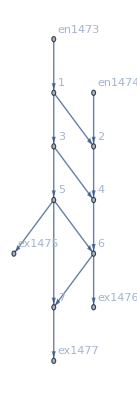

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
MFGEquations["FG"]
```

```mathematica
MFGEquations["EqAll"]/.(MFGEquations["criticalreduced1"][[2]])
```

True

```mathematica
Chop/@MFGEquations["criticalreduced1"][[2]]
```

<|j1478→0,j1479→2,j1481→0,j1482→2,j1486→2,j1488→2,j1489→0,j1490→2,j1491→2,j1492→0,j1493→0,j1494→0,j1495→0,j1496→0,j1497→0,j1498→0,j1499→0,j1500→0,j1502→0,j1503→0,j1504→0,j1505→0,jt1506→0,jt1507→0,jt1508→0,jt1509→0,jt1510→0,jt1511→2,jt1513→0,jt1514→0,jt1515→0,jt1516→0,jt1517→2,jt1520→0,jt1521→0,jt1522→0,jt1523→0,jt1524→0,jt1526→0,jt1527→0,jt1529→0,jt1532→2,jt1534→0,jt1535→0,jt1537→0,jt1538→0,jt1539→0,jt1540→0,jt1541→0,jt1542→0,jt1544→2,jt1545→0,jt1546→0,jt1547→0,jt1550→0,jt1551→0,jt1552→0,jt1553→0,jt1554→0,jt1555→0,jt1557→0,jt1558→0,jt1559→0,u1560→5,u1561→5,u1562→5,u1563→3,u1564→3,u1565→3,u1566→1,u1567→1,u1568→1,u1570→1,u1571→1,u1574→5,u1575→3,u1576→3,u1577→3,u1578→1,u1579→1,u1580→1,u1581→1,u1582→1,u1583→1,u1584→1,u1585→1,u1586→5,u1587→5,j1480→2,j1483→2,j1484→0,j1485→0,j1487→0,j1501→0,jt1512→0,jt1518→0,jt1519→2,jt1525→2,jt1528→0,jt1530→0,jt1531→0,jt1533→0,jt1536→0,jt1543→0,jt1548→0,jt1549→0,jt1556→0,u1569→1,u1572→5,u1573→5|>

```mathematica
Chop/@(MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]])
```

<|{2,1->2}→0,{3,1->3}→2,{4,2->4}→2,{4,3->4}→0,{5,3->5}→2,{6,4->6}→2,{6,5->6}→0,{7,5->7}→0,{ex1475,5->ex1475}→2,{7,6->7}→0,{ex1476,6->ex1476}→2,{ex1477,7->ex1477}→0,{1,en1473->1}→2,{2,en1474->2}→2,{1,1->2}→0,{1,1->3}→0,{2,2->4}→0,{3,3->4}→0,{3,3->5}→0,{4,4->6}→0,{5,5->6}→0,{5,5->7}→0,{5,5->ex1475}→0,{6,6->7}→0,{6,6->ex1476}→0,{7,7->ex1477}→0,{en1473,en1473->1}→0,{en1474,en1474->2}→0|>

#### Non-linear case

```mathematica
alpha = .99;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

$Aborted

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->#,PlotRange->{-0.1,2.4},GridLines->Automatic]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->#,PlotRange->{1-0.1,4.7},GridLines->Automatic]&/@MFGEquations["BEL"]
```